# Zapori v Evropki uniji

Datum : 23. 3. 2021

## Podatki, ki jih bomo uporabili:

```mathematica
drzaveEvropa = CountryData["Europe", "Name"](*Vse evropske države.*)
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,North Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
drzaveEU = CountryData["EU", "Name"] (*Vse države Evropske Unije.*);
```

```mathematica
steviloZapornikovEvropa = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\persons_held_total.xlsx"][[1]];
```

```mathematica
evropskeDrzaveZaporniki = Select[steviloZapornikovEvropa, #[[1]]=="Europe"&];
popolniPodatkiEvropa = Select[evropskeDrzaveZaporniki, !MemberQ[#,""]&](*Vrstice z vsemi podatki*)
```

{{Europe,Eastern Europe,Belarus,UN-CTS/NSO,48434.,500.4,42253.,439.4,40878.,427.5,44812.,470.9,45695.,482.,43349.,458.6,40186.,426.,39627.,420.6,36652.,389.3,28841.,306.3,28471.,302.1,29776.,315.7,33329.,353.1,35169.,372.3,34356.,363.6,32556.,344.4},{Europe,Eastern Europe,Bulgaria,UN-CTS,10066.,129.,10871.,140.4,11436.,148.8,11058.,144.9,10271.,135.6,9408.,125.,9006.,120.5,9379.,126.3,9885.,134.,9493.,129.4,8834.,121.2,7870.,108.6,7408.,102.9,7345.,102.7,6988.,98.4,6651.,94.3},{Europe,Eastern Europe,Czechia,UN-CTS,17277.,168.7,18343.,179.1,18937.,184.6,18578.,180.4,18901.,182.5,20502.,196.7,21734.,207.2,21900.,207.8,23170.,219.3,22644.,214.,16645.,157.2,18658.,176.2,20866.,196.8,22481.,211.7,22159.,208.2,21577.,202.3},{Europe,Eastern Europe,Hungary,UN-CTS,16860.,166.3,16546.,163.6,15755.,156.2,14822.,147.4,14353.,143.2,14743.,147.5,15432.,155.,16328.,164.5,17210.,173.9,17179.,174.2,17841.,181.4,17890.,182.5,17449.,178.5,17658.,181.1,17343.,178.2,16947.,174.6},{Europe,Eastern Europe,Poland,UN-CTS,79281.,206.2,80368.,209.3,84875.,221.2,90529.,236.,89648.,233.7,84978.,221.5,85749.,223.6,82372.,214.9,82832.,216.3,85459.,223.6,80165.,210.1,79345.,208.3,72695.,191.1,72209.,190.1,74480.,196.2,72818.,192.},{Europe,Eastern Europe,Romania,UN-CTS,42815.,197.1,39031.,180.9,36700.,171.4,34038.,160.3,29390.,139.7,26212.,125.8,26716.,129.5,28244.,138.,30694.,150.9,31817.,157.3,33434.,166.1,30156.,150.5,28334.,142.2,27455.,138.7,23450.,119.3,20792.,106.6},{Europe,Eastern Europe,Slovakia,UN-CTS,8873.,164.3,9422.,174.5,8897.,164.8,8249.,152.8,7986.,147.9,8166.,151.3,9316.,172.5,10031.,185.6,10525.,194.6,10850.,200.4,9753.,179.9,10020.,184.6,9913.,182.4,9995.,183.7,10028.,184.1,10294.,188.8},{Europe,Northern Europe,Denmark,UN-CTS,3641.,67.6,3767.,69.7,4041.,74.5,3932.,72.2,3624.,66.3,3451.,62.8,3721.,67.3,3944.,71.,3947.,70.7,3829.,68.2,4091.,72.6,3583.,63.3,3203.,56.3,3408.,59.7,3418.,59.6,3635.,63.2},{Europe,Northern Europe,Estonia,UN-CTS,4576.,333.3,4565.,334.7,4410.,325.2,4310.,319.5,3456.,257.1,3656.,272.8,3555.,266.1,3393.,254.7,3400.,256.,3286.,248.4,3112.,235.9,3034.,230.5,2823.,214.7,2864.,217.5,2723.,206.4,2584.,195.3},{Europe,Northern Europe,Finland,UN-CTS,3641.,69.7,3704.,70.7,3867.,73.5,3851.,73.,3625.,68.4,3530.,66.4,3589.,67.2,3364.,62.7,3268.,60.6,3306.,61.1,3295.,60.6,3148.,57.6,3135.,57.2,3156.,57.4,3082.,55.9,2956.,53.5},{Europe,Northern Europe,Ireland,UN-CTS,3234.,81.3,3162.,77.9,3022.,73.,3080.,72.8,3253.,75.2,3484.,78.9,3868.,86.1,4318.,94.8,4216.,91.8,4287.,93.,4088.,88.6,3777.,81.6,3722.,80.,3718.,79.2,3680.,77.4,3962.,82.2},{Europe,Northern Europe,Latvia,UN-CTS,8305.,360.1,8231.,361.2,7646.,339.5,6965.,313.,6548.,297.9,6548.,301.6,7055.,328.9,6780.,320.,6561.,313.3,6117.,295.7,5136.,251.1,4745.,234.8,4409.,220.7,4243.,214.9,3765.,193.,3522.,182.7},{Europe,Northern Europe,Lithuania,UN-CTS,8063.,236.2,8125.,240.3,8137.,243.3,8079.,244.6,7866.,241.4,8000.,249.,8655.,273.3,9139.,292.5,9920.,321.8,9729.,319.4,9261.,307.8,8636.,290.7,7355.,250.9,6815.,235.8,6599.,232.,6485.,231.5},{Europe,Northern Europe,Sweden,UN-CTS,6755.,75.5,7332.,81.5,7377.,81.6,7397.,81.3,6977.,76.1,7073.,76.6,7286.,78.2,6846.,72.9,6669.,70.4,6296.,66.,5723.,59.5,5807.,59.9,5691.,58.3,5658.,57.5,5713.,57.7,6114.,61.3},{Europe,Northern Europe,United Kingdom (England and Wales),UN-CTS,73657.,139.3,74488.,140.1,75121.,140.2,76560.,141.9,78445.,144.2,81674.,148.9,81836.,148.2,84004.,150.8,84428.,150.3,84886.,150.1,81884.,143.8,83678.,145.8,84444.,145.9,83604.,143.5,84441.,143.9,81904.,138.6},{Europe,Northern Europe,United Kingdom (Scotland),UN-CTS,6606.,130.3,6776.,133.3,6856.,134.2,7187.,140.,7376.,142.7,7827.,150.4,7964.,152.2,7854.,149.3,8179.,154.3,8057.,151.6,7894.,148.2,7731.,144.6,7744.,144.1,7579.,140.,7436.,136.7,7788.,142.5},{Europe,Southern Europe,Albania,UN-CTS,2561.,82.1,2321.,74.8,2592.,84.,2857.,93.3,2790.,92.,4916.,163.7,4667.,157.,4657.,158.,4659.,159.1,4618.,158.5,4998.,172.1,5689.,196.4,5981.,206.9,6031.,209.,5674.,196.7,5316.,184.4},{Europe,Southern Europe,Croatia,UN-CTS,2805.,63.9,3029.,69.1,3485.,79.6,3833.,87.7,4290.,98.3,4734.,108.8,4891.,112.7,5165.,119.3,5084.,117.9,4741.,110.4,4352.,101.8,3763.,88.4,3341.,78.9,3108.,73.8,3190.,76.3,3217.,77.4},{Europe,Southern Europe,Greece,UN-CTS/WPB-ICPR,8726.,77.8,8722.,77.6,9964.,88.8,10370.,92.7,11645.,104.7,11736.,106.3,11364.,103.7,12349.,113.4,12479.,115.2,12475.,115.7,12693.,118.2,11798.,110.3,9611.,90.2,9560.,90.1,10011.,94.7,10654.,101.3},{Europe,Southern Europe,Italy,UN-CTS,54993.,95.5,56903.,98.2,60415.,103.7,39794.,68.,49697.,84.6,59284.,100.6,65598.,111.,69263.,116.8,68325.,114.7,67102.,112.1,63848.,106.1,54745.,90.6,53410.,88.2,55978.,92.3,59038.,97.3,61131.,100.8},{Europe,Southern Europe,Malta,UN-CTS/NSO,278.,69.3,298.,73.9,294.,72.6,375.,92.4,528.,129.4,662.,161.9,494.,119.9,584.,141.1,584.,139.7,585.,138.6,615.,144.4,581.,135.1,569.,131.1,553.,126.8,591.,134.9,619.,141.},{Europe,Southern Europe,Montenegro,UN-CTS,741.,120.7,799.,129.9,894.,145.1,851.,137.7,957.,154.4,1216.,195.8,1499.,240.6,1457.,233.5,1328.,212.5,1331.,212.6,1064.,170.,1123.,179.1,1131.,180.4,1123.,179.1,1119.,178.2,1125.,179.1},{Europe,Southern Europe,Portugal,UN-CTS,13835.,132.6,13152.,125.6,12889.,122.7,12636.,119.9,11587.,109.6,10807.,102.,11287.,106.4,11839.,111.7,12955.,122.6,13875.,131.8,14535.,138.8,14198.,136.3,14373.,138.6,13917.,134.8,13587.,132.1,13021.,127.},{Europe,Southern Europe,Serbia,UN-CTS/WPB-ICPR,7487.,98.7,7654.,101.5,8078.,107.9,7893.,106.3,9043.,122.7,9701.,132.7,10975.,151.1,11211.,155.4,11070.,154.3,10226.,143.3,10031.,141.4,10288.,145.4,10064.,142.2,10672.,151.6,10807.,154.4,10871.,156.4},{Europe,Southern Europe,Slovenia,UN-CTS,1070.,53.8,1085.,54.5,1132.,56.7,1301.,65.,1336.,66.4,1318.,65.2,1365.,67.1,1351.,66.1,1273.,62.1,1377.,66.9,1360.,65.9,1522.,73.6,1399.,67.6,1308.,63.1,1316.,63.4,1396.,67.2},{Europe,Southern Europe,Spain,UN-CTS,56096.,131.7,59375.,137.1,61054.,138.7,64021.,143.1,67100.,147.7,73558.,159.7,76079.,163.3,73929.,157.5,70472.,149.7,68597.,145.8,66765.,142.3,65017.,139.,61614.,132.,59589.,127.8,58814.,126.1,58883.,126.1},{Europe,Western Europe,Germany,UN-CTS,80829.,99.,80933.,99.1,80201.,98.3,78063.,95.8,75153.,92.5,73793.,91.,72295.,89.4,70827.,87.6,69543.,86.,68533.,84.6,66221.,81.6,63228.,77.6,63020.,77.1,64291.,78.2,65841.,79.7,65762.,79.1},{Europe,Western Europe,Netherlands,UN-CTS,16184.,99.9,18766.,115.2,17560.,107.3,16091.,97.9,15151.,91.8,14610.,88.2,14364.,86.4,14368.,86.1,13969.,83.5,13473.,80.2,12721.,75.5,11934.,70.6,10850.,64.1,10601.,62.4,10874.,63.9,11251.,65.9},{Europe,Western Europe,Switzerland,UN-CTS,4842.,66.6,5509.,75.2,5723.,77.5,5567.,74.6,5278.,70.,5303.,69.6,5605.,72.7,5765.,73.8,5626.,71.2,6102.,76.2,6634.,81.8,6519.,79.4,6498.,78.3,6507.,77.6,6564.,77.6,6602.,77.4}}

```mathematica
steviloZapornikovAbs = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_absolutno.xlsx"][[1]];
```

```mathematica
jeVEU[x_]:= MemberQ[drzaveEU, CountryData[x]]; (*Funkcija preveri ali je država članica EU.*)
```

```mathematica
drzaveEUZaporniki =Select[steviloZapornikovAbs,MemberQ[drzaveEU, #[[1]]]&];
```

```mathematica
zapornikiSlovenija0318ABS = Select[steviloZapornikovEvropa, #[[3]] == "Slovenia"&][[1]][[5;;-1;;2]];(*Seznam absolutnih vrednosti števila zapornikov med leti 2003 - 2018 v republiki Sloveniji.*)
```

```mathematica
zapornikiSlovenija0318Rel = Select[steviloZapornikovEvropa, #[[3]] == "Slovenia"&][[1]][[6;;-1;;2]];
(*Seznam relativnih vrednosti števila zapornikov na 100.000 prebivalcev v republiki Sloveniji.*)
```

{53.8,54.5,56.7,65.,66.4,65.2,67.1,66.1,62.1,66.9,65.9,73.6,67.6,63.1,63.4,67.2}

```mathematica
zapornikiSlovenija = Select[steviloZapornikovAbs, #[[1]] == "Slovenia"&];
```

```mathematica
zapornikiSlovenija[[1]][[2;;Length[zapornikiSlovenija[[1]]]]]; (*Število zaprtih po letih v Slovenije med leti 2009 in 2018*)
```

```mathematica
zapornikiSlovenijaTS0318Rel = TimeSeries[zapornikiSlovenija0318Rel,{Range[2003, 2018]}];
```

TimeSeries[…]

```mathematica
zapornikiSlovenijaTS0318ABS = TimeSeries[zapornikiSlovenija0318ABS,{Range[2003, 2018]}];
(* Časovna vrsta absolutnega števila zapornikov v republiki Sloveniji med leti 2003 in 2018*)
```

```mathematica
(*zapornikiSlovenijaTS = TimeSeries[zapornikiSlovenija[[1]][[2;;Length[zapornikiSlovenija[[1]]]]], {Range[2009, 2018]}](*Časovna vrsta zaporniki Slovenija.*)*)
```

```mathematica
(*ListLinePlot[zapornikiSlovenijaTS, PlotLabel->Style["Število zaprtih oseb v Sloveniji med leti 2003 in 2018", 16, Darker[Blue], Background->Lighter[Yellow]], ImageSize->Large, PlotTheme->"Detailed"]*)
```

ListLinePlot::lpn: zapornikiSlovenijaTS is not a list of numbers or pairs of numbers.

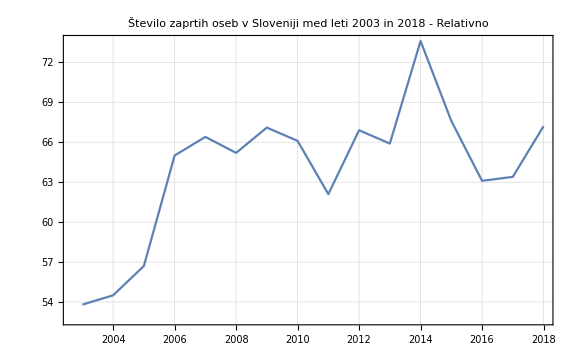

```mathematica
ListLinePlot[zapornikiSlovenijaTS0318Rel,PlotLabel->"Število zaprtih oseb v Sloveniji med leti 2003 in 2018 - Relativno",ImageSize->Large,PlotTheme->"Detailed"]
```

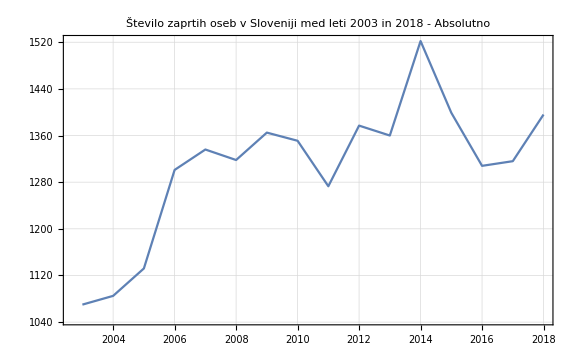

```mathematica
ListLinePlot[zapornikiSlovenijaTS0318ABS,PlotLabel->"Število zaprtih oseb v Sloveniji med leti 2003 in 2018 - Absolutno",ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
s = steviloZapornikovAbs[[1]];
```

```mathematica
steviloZapornikovEU1 = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_po_drzavi.xlsx", {"Data", 5, Range[9, 51]}];
```

```mathematica
stZaprtiPoLetuEU = Select[steviloZapornikovEU, MemberQ[drzaveEU,#[[0]]]&]
```

{}

```mathematica
steviloZapornikovEU = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_po_drzavi.xlsx"];
```

```mathematica
steviloZapornikovEU[[5]]//Grid;
```